```mathematica
α[r_]:=9/2-2/3 Exp[-2r](r^5+9/2 r^4+9 r^3+27/2 r^2+27/2 r+27/4);
```

```mathematica
Series[α[r]/r^4,{r,∞,5}]
```

(9/(2 r^4)+O[1/r]^6)+ⅇ^(-2 r+O[1/r]^11) (-(2 r)/3-3-6/r-9/r^2-9/r^3-9/(2 r^4)+O[1/r]^6)

```mathematica
Series[Exp[-2r] r^5,{r,∞,3}]
```

ⅇ^(-2 r+O[1/r]^4) (r^5+O[1/r]^4)

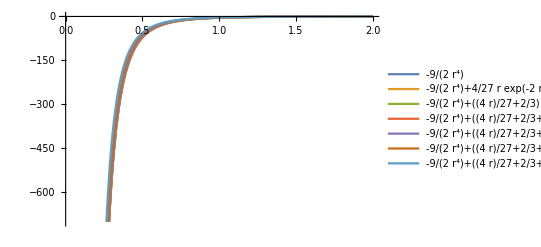

```mathematica
Plot[{-9/(2 r^4),-9/(2 r^4)+4/27 r Exp[-2r],-9/(2 r^4)+(4/27 r+ 2/3)Exp[-2r],-9/(2 r^4)+(4/27 r+ 2/3+4/(3r))Exp[-2r],-9/(2 r^4)+(4/27 r+ 2/3+4/(3r)+2/r^2)Exp[-2r],-9/(2 r^4)+(4/27 r+ 2/3+4/(3r)+2/r^2+2/r^3)Exp[-2r],-9/(2 r^4)+(4/27 r+ 2/3+4/(3r)+2/r^2+2/r^3+1/r^4)Exp[-2r]},{r,0,2},PlotLegends->"Expressions"]
```

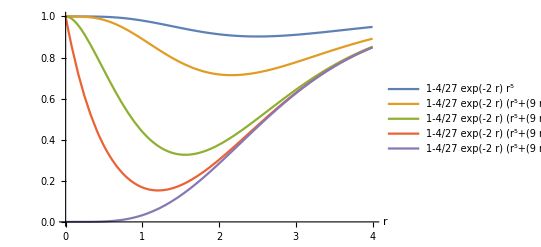

```mathematica
f[r_]:=9/2;
Plot[{1-4/27 Exp[-2r] r^5,1-4/27 Exp[-2r](r^5+9/2 r^4),1-4/27 Exp[-2r](r^5+9/2 r^4+9 r^3+27/2 r^2),1-4/27 Exp[-2r](r^5+9/2 r^4+9 r^3+27/2 r^2+27/2 r),1-4/27 Exp[-2r](r^5+9/2 r^4+9 r^3+27/2 r^2+27/2 r+27/4)},{r,0,4},PlotLegends->"Expressions",AxesLabel->{"r"}]
```

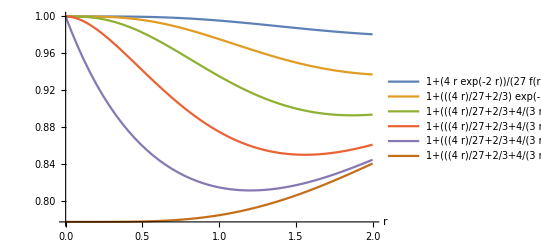

```mathematica
ⅇ^(-2 r+O[1/r]^4) (r^5+O[1/r]^4)
```

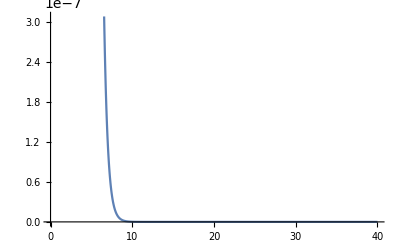

```mathematica
Plot[Exp[-2r]/r,{r,0, 40},PlotRange->Automatic]
```

```mathematica
1/(200*5^2)//N
```

0.0002